```mathematica
(*resolucion de la acrecion como eq diferencial sola*)
```

```mathematica
f2[x_?NumericQ]:= σ*x^2*(1+x^2)^(-5/2)
```

```mathematica
mb := m0 * ab
Msol := 1989*10^(30) (*en gramos*)
m0 := 10^4*Msol 
m0 //N
ab := Rationalize[7.41*10^(-9), 0] (*adimensional*)
ηb := Rationalize[2.19*10^4,0]  (*en segundos*)
ηi := Rationalize[2.96*10^(12),0]   (*en segundos*)
G := 6.674*10^(-8)  (*en cgs*)
c := 2.998*10^(10)   (*en cgs*)
σ :=Rationalize[(81*G)/(8*c^3)*1/(ab*ηb), 0]
xi :=Rationalize[ηi/ηb, 0]
```

1.989×10^37

```mathematica
N[σ]
```

1.54534×10^-34

```mathematica
(* solucion analitica *)
```

```mathematica
g[x_]:=(σ*x^3)/(3*(x^2+1)^(3/2))
gf[x_]:=x^3/(3*(x^2+1)^(3/2))
Man[x_] := 1/(1/m0-(g[x]-g[xi]))
```

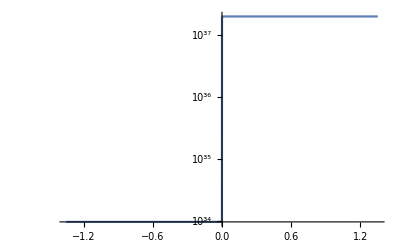

```mathematica
LogPlot[Man[x],{x,-xi,xi}, PlotRange->All]
```

```mathematica
Man[xi]
```

19890000000000000000000000000000000000

```mathematica
ScientificForm[N[19890000000000000000000000000000000000]]
```

1.989×10^37

```mathematica
Man[-xi]
```

1/(1/19890000000000000000000000000000000000+25934336000000000000000000000000/(8504536615947464460186557301543383501554829007947639517 √876160000000000047961))

```mathematica
ScientificForm[N[1/(1/19890000000000000000000000000000000000+25934336000000000000000000000000/(8504536615947464460186557301543383501554829007947639517 √876160000000000047961))]]
```

9.70187×10^33

```mathematica
Man[0]
```

1/(1/19890000000000000000000000000000000000+12967168000000000000000000000000/(8504536615947464460186557301543383501554829007947639517 √876160000000000047961))

```mathematica
ScientificForm[N[1/(1/19890000000000000000000000000000000000+12967168000000000000000000000000/(8504536615947464460186557301543383501554829007947639517 √876160000000000047961))]]
```

1.93943×10^34

```mathematica
dMdx =  NDSolve[{y'[x]==σ*x^2*1/((1+x^2)^(5/2))*y[x]^2,y[xi]==m0},y,{x,-xi,xi}, Method->{"ExplicitRungeKutta","DifferenceOrder"->5},MaxSteps->Infinity,PrecisionGoal->20,WorkingPrecision->40,AccuracyGoal->20 ]
```

{{y→                                                                     8                                              8
InterpolatingFunction[{{-1.351598173515981735159817351598173515982 10 , 1.351598173515981735159817351598173515982 10 }}, <>]}}

```mathematica
LogPlot[y[x]/.dMdx,{x,-xi,xi}, PlotRange->All]
```

-Graphics-

```mathematica
y[-xi]/.dMdx
```

{9.70186758792300010357473895259944531232×10^33}

```mathematica
N[1/(1/19890000000000000000000000000000000000+12967168000000000000000000000000/(8504536615947464460186557301543383501554829007947639517 √876160000000000047961))]
```

1.93943×10^34

```mathematica
y[0]/.dMdx
```

{1.93942751110349890420300724239224270799×10^34}

```mathematica
(*ESTO DE ACA NO SIRVE*)
```

```mathematica
"StiffnessTest"->False
Plot[{Man[x],y[x]/.mx},{x,-10,10},PlotLegends->{"Analítica","Numérica"}]
```

```mathematica
Mnum[x_]:= (y[x]/. First[mx])
```

```mathematica
Chop[ Mnum[10]- Man[10]]
```

InterpolatingFunction::dmval: Input value {10} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/0. encountered.

Power::indet: Indeterminate expression 0.^0. encountered.

Power::infy: Infinite expression 1/0. encountered.

Power::indet: Indeterminate expression 0.^0. encountered.

3.×10^431-1/(1/19890000000000000000000000000000000000-500/(980366825934411367169773727190899097 √101)+12967168000000000000000000000000/(8504536615947464460186557301543383501554829007947639517 √876160000000000047961))

```mathematica
dMdx=
```

```mathematica
Plot[Abs[Man[x]-y[x]/.mx]/Man[x],{x,-10,10},PlotRange->All]
```

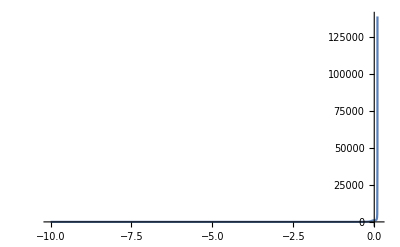
```mathematica
-Graphics-dMdx=
```

```mathematica
λ:= σ*m0
dudx= NDSolve[{y'[x]==λ*x^2*(1+x^2)^(-5/2)*y[x]^2,y[0]==1},y,{x,-1,1}, Method->{"ExplicitRungeKutta","DifferenceOrder"->5},MaxSteps->Infinity,PrecisionGoal->20,WorkingPrecision->40,AccuracyGoal->20 ]
```

NDSolve::ndsz: At x == 0.09968612005969604284833034910975101629912, step size is effectively zero; singularity or stiff system suspected.

{{y→InterpolatingFunction[{{-1.000000000000000000000000000000000000000, 0.09968612005969604284833034910975101629912}}, <>]}}

```mathematica
LogPlot[y[x]/.dudx,{x,-1,1}, PlotRange->All]
```

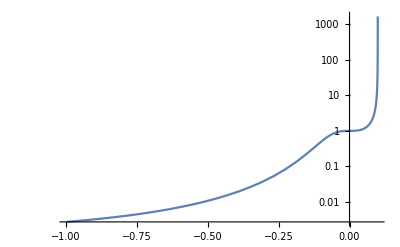
```mathematica
-Graphics-□"StiffnessTest"->False
```

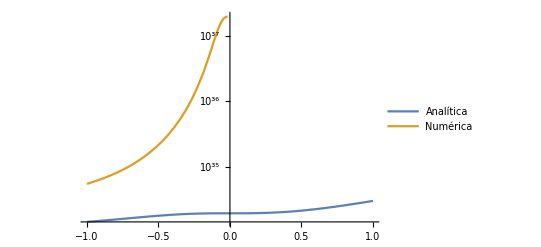

```mathematica
LogPlot[{Man[x],m0*y[x]/.dudx},{x,-1,1},PlotLegends->{"Analítica","Numérica"}]
```

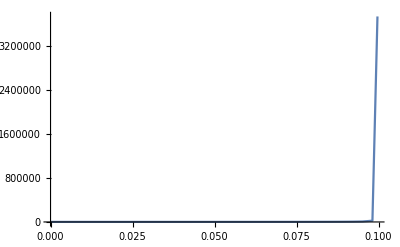

```mathematica
Plot[Abs[Man[x]-m0*y[x]/.dudx]/Man[x],{x,0,10},PlotRange->All]
```

```mathematica
dzdx= NDSolve[{y'[x]==-λ*x^2*1/((1+x^2)^(5/2)),y[0]==1},y,{x,-1,10}, Method->{"ExplicitRungeKutta","DifferenceOrder"->5},MaxSteps->Infinity,PrecisionGoal->20,WorkingPrecision->40,AccuracyGoal->20 ]
```

{{y→InterpolatingFunction[{{-1.000000000000000000000000000000000000000, 10.00000000000000000000000000000000000000}}, <>]}}

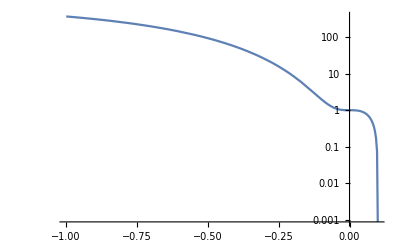

```mathematica
LogPlot[(y[x]/.dzdx),{x,-1,10}, PlotRange->All]
```

```mathematica
LogPlot[(y[x]/.dzdx)^(-1),{x,-1,1}, PlotRange->All]
```

-Graphics-